```mathematica
Needs["Cosmology`"]
```

```mathematica
Convert[HubbleConstant, 1/Second]
```

3.24077928966×10^-18 Second^-1

## Initialization

```mathematica
(* Switch to the directory the notebook and data files are in *)
SetDirectory[NotebookDirectory[]]
```

/Users/npadmana/myWork/np_sandbox/diff_transfer_fn

```mathematica
(* Number of files *)
```

```mathematica
nfiles = 5;
```

```mathematica
(* zvals -- hardcoded is not ideal, but why not?? *)
```

```mathematica
zvals= {0.04, 0.03, 0.02, 0.01, 0.00};
```

```mathematica
(* Set the file name list *)
```

```mathematica
fnames = "test_transfer_z"<>ToString[#]<>".dat"& /@ Range[0,nfiles-1];
```

```mathematica
(* Read in all the files *)
```

```mathematica
tData = Import[#, "Table"] & /@ fnames;
```

```mathematica
Dimensions[tData]
```

{5,692,7}

```mathematica
kval = tData[[1,All,1]];
```

```mathematica
transfers = tData[[All, All, {2,3}]];
```

```mathematica
Dimensions[transfers]
```

{5,692,2}

### Normalization

The CAMB transfer functions are normalized to make it easy to compute power spectra, but this is inconvenient when computing derivatives of transfer functions. So let us remove and store the normalizations. I

```mathematica
norms = transfers[[All, 1, All]]
```

{{1.99711×10^7,1.99711×10^7},{2.00696×10^7,2.00696×10^7},{2.01684×10^7,2.01684×10^7},{2.02675×10^7,2.02675×10^7},{2.03668×10^7,2.03668×10^7}}

```mathematica
tNorm = Transpose[ Transpose[transfers, {1,3,2}]/norms, {1,3,2}];
```

```mathematica
Dimensions[tNorm]
```

{5,692,2}

```mathematica
(* We can do this more cleverly, by precomputing coefficients, but not today *)
```

```mathematica
D[Fit[Thread[{zvals, tNorm[[All,100, 2]]}], {1, z, z^2}, z],z] /. z->0
```

-0.0000321601

```mathematica
(* This derivative is wrt z, we want the derivative wrt t)
```

```mathematica
z[t_] := 1/a[t] - 1;
```

```mathematica
D[z[t], t]
```

-a'[t]/a[t]^2

```mathematica
(* This is nothing but the Hubble constant divided by the scale factor, which for z=0 is 1 *)
(* However looking ahead the only thing we need are dimensionless values so lets drop this for now *)
```

```mathematica
tBaryDot=D[Fit[Thread[{zvals, tNorm[[All,#, 2]]}], {1, z}, z],z]/.z->0 & /@ Range[Dimensions[tNorm][[2]]];
```

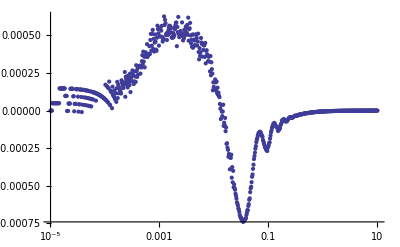

```mathematica
ListLogLinearPlot[Thread[{kval, tBaryDot}]]
```

```mathematica
(* We'll probably want to remove some of the noise in this, but this should be fine to begin *)
```